#### Some useful constants

```mathematica
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
m={12.0107,91.224,1};ang2bohr=1/0.529177208;ev2har=1/27.211396;eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
```

#### DFT data: energy-volume and energy-displacement numbers

```mathematica
(*Volumes and energies*)
volperf={766.060875,778.68799,791.45312,808.7083508,822.6569529,846.5905360,862.257739832,885.289075,912.67299};e0perf={-.67382051*10^3,-.67479111*10^3,-.67540188*10^3,-.67568572*10^3,-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};e0cvac={-.66257856,-.66353617,-.66414458,-.66444074,-.66427725,-.66324766,-.66211597,-.65987660,-.65643966}*10^3;

(*Import V-nn (Zr) and V-nnn (C) data *)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS"]
filesC={"4.575.C.out","4.600.C.out","4.625.C.out","4.65837.C.out","4.685.C.out","4.730.C.out","4.759.C.out","4.801.C.out","4.850.C.out"};filesZr={"4.575.Zr.out","4.600.Zr.out","4.625.Zr.out","4.65837.Zr.out","4.685.Zr.out","4.730.Zr.out","4.759.Zr.out","4.801.Zr.out","4.850.Zr.out"};
CdataFull=Table[ReadList[filesC[[i]],{Number,Number,Word,Word,Number,Number,Number,Number}],{i,1,Length@filesC}];ZrdataFull=Table[ReadList[filesZr[[i]],{Number,Number,Word,Word,Number,Number,Number,Number}],{i,1,Length@filesZr}];Cdata=Table[Transpose@{Transpose[CdataFull[[vol]]][[1]],1000*Transpose[CdataFull[[vol]]][[8]]}//N,{vol,1,Length@filesC}];Zrdata=Table[Transpose@{Transpose[ZrdataFull[[vol]]][[1]],1000*Transpose[ZrdataFull[[vol]]][[8]]}//N,{vol,1,Length@filesZr}];
(*Import Perfect data*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"]
filesCperf={"C_4575","C_4600","C_4625","C_46583","C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4575_110","C_4600_110","C_4625_110","C_46583_110","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4575_111","C_4600_111","C_4625_111","C_46583_111","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZrperf={"Zr_4575","Zr_4600","Zr_4625","Zr_46583","Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4575_110","Zr_4600_110","Zr_4625_110","Zr_46583_110","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4575_111","Zr_4600_111","Zr_4625_111","Zr_46583_111","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};

CdataPerf=Table[ReadList[filesCperf[[i]],{Number, Number}],{i,1,27}];
ZrdataPerf=Table[ReadList[filesZrperf[[i]],{Number, Number}],{i,1,27}];
```

/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS

/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols

#### Some notes - delete later

```mathematica
(*(*Types of direction*)(**)(*Degeneracies in perfect*)
(*001:3,011:6,111:4*)
(*Degeneracies in Cvac for C*)(*Note y is missing for 001 C+*)
(*001:3:2(u,x&z)|1(g,y),011:6:5(u,2xy&2yz&1xy)|1(bxz),111:4:2(u)|2(g)*)
(*Degeneracies in Cvac for Zr*)(*001::3:1(u,x)|2(g,y&z),011::6:2(g,yz)|4(u,xz&&xy),111:4:4(u,xyz)*)
```

```mathematica
labelsC=Transpose[Table[Partition[CdataFull[[1]],Length@CdataFull[[1]]/6][[i]][[1]],{i,1,6}]][[4]]//TableForm;
labelsCperf={"x","xy","xyz"};
labelsZr=Transpose[Table[Partition[ZrdataFull[[1]],Length@ZrdataFull[[1]]/5][[i]][[1]],{i,1,5}]][[4]]//TableForm;
labelsZrperf={"x","xy","xyz"};
(*
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>cat 4.685.C.out|awk'{print $4}'|uniq
100/x
100/y
110/xy
110/xz
111/bxyz
111/xyz
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>cat 4.685.Zr.out|awk'{print $4}'|uniq
100/x
100/y
110/xz
110/yz
111/xyz
tamellan_mba:/Volumes/MicroSD/2_PostDoc_SD/Einstein/Data/Einstein_oscillator_4685Ang_ZrC/Full_CVAC_RESULTS>
*)
```

#### Make the presentation of data palatable - separate diff directions

```mathematica
(*Note I'm chopping off all the data beyond 0.8, as it seems quitre anharmonic*)
trimmer[arg_]:=Table[DeleteCases[Table[If[Norm[arg[[j]][[i]][[1]]]>0.8,{0,0},arg[[j]][[i]]],{i,1,Length@arg[[j]]}],{0,0}],{j,1,Length@arg}]
CdataX=trimmer@Table[Partition[Cdata[[i]],65][[1]],{i,1,9}];
CdataY=trimmer@Table[Partition[Cdata[[i]],65][[2]],{i,1,9}];CdataXY=trimmer@Table[Partition[Cdata[[i]],65][[3]],{i,1,9}];CdataXZ=trimmer@Table[Partition[Cdata[[i]],65][[4]],{i,1,9}];CdataBXYZ=trimmer@Table[Partition[Cdata[[i]],65][[5]],{i,1,9}];CdataXYZ=trimmer@Table[Partition[Cdata[[i]],65][[6]],{i,1,9}];cdataAllDir={CdataX,CdataY,CdataXY,CdataXZ,CdataBXYZ,CdataXYZ};
cdataAllDirNames={"CdataX","CdataY","CdataXY","CdataXZ","CdataBXYZ","CdataXYZ"};ZrdataX=trimmer@Table[Partition[Zrdata[[i]],65][[1]],{i,1,9}];ZrdataY=trimmer@Table[Partition[Zrdata[[i]],65][[2]],{i,1,9}];ZrdataXY=trimmer@Table[Partition[Zrdata[[i]],65][[3]],{i,1,9}];ZrdataYZ=trimmer@Table[Partition[Zrdata[[i]],65][[4]],{i,1,9}];ZrdataXYZ=trimmer@Table[Partition[Zrdata[[i]],65][[5]],{i,1,9}];zrdataAllDir={ZrdataX,ZrdataY,ZrdataXY,ZrdataYZ,ZrdataXYZ};
zrdataAllDirNames={"ZrdataX","ZrdataY","ZrdataXY","ZrdataYZ","ZrdataXYZ"};

(*Perfect*)

CdataPerfX=trimmer@CdataPerf[[1;;9]];
CdataPerfXY=trimmer@CdataPerf[[10;;18]];
CdataPerfXYZ=trimmer@CdataPerf[[19;;27]];
cdataPerfAllDir={CdataPerfX,CdataPerfXY,CdataPerfXYZ};
cdataPerfAllDirNames={"CdataPerfX","CdataPerfXY","CdataPerfXYZ"};

ZrdataPerfX=trimmer@ZrdataPerf[[1;;9]];
ZrdataPerfXY=trimmer@ZrdataPerf[[10;;18]];
ZrdataPerfXYZ=trimmer@ZrdataPerf[[19;;27]];
zrdataPerfAllDir={ZrdataPerfX,ZrdataPerfXY,ZrdataPerfXYZ};
zrdataPerfAllDirNames={"ZrdataPerfX","ZrdataPerfXY","ZrdataPerfXYZ"};
```

#### Plot the DFT data along various directions for each environment

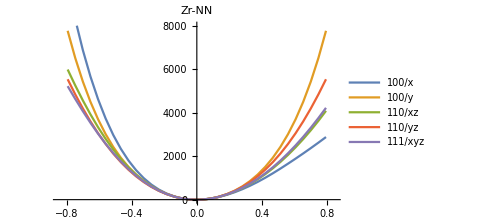

```mathematica
ListLinePlot[Table[zrdataAllDir[[i]][[5]],{i,1,5}],PlotRange->{{-0.85,0.85},{0,8000}},ImageSize->Medium,PlotLegends->Table[labelsZr[[i]],{i,1,Length@labelsZr}],PlotLabel->"Zr-NN"]
```

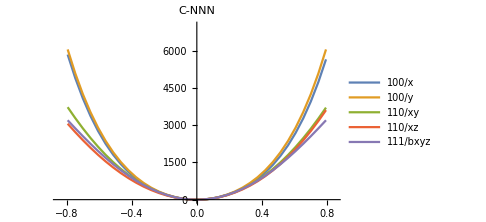

```mathematica
ListLinePlot[Table[cdataAllDir[[i]][[5]],{i,1,5}],PlotRange->{{-0.85,0.85},{0,7000}},ImageSize->Medium,PlotLegends->Table[labelsC[[i]],{i,1,Length@labelsC}],PlotLabel->"C-NNN"]
```

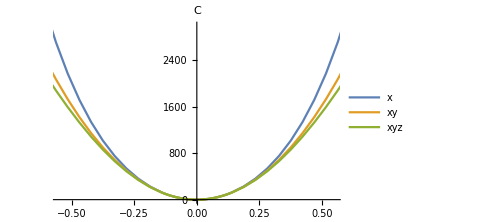

```mathematica
ListLinePlot[Table[cdataPerfAllDir[[i]][[5]],{i,1,3}],PlotRange->{{-0.55,0.55},{0,3000}},ImageSize->Medium,PlotLegends->Table[labelsCperf[[i]],{i,1,Length@labelsCperf}],PlotLabel->"C"]
```

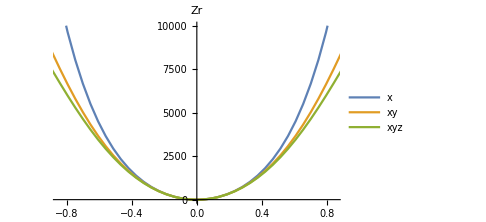

```mathematica
ListLinePlot[Table[zrdataPerfAllDir[[i]][[5]],{i,1,3}],PlotRange->{{-0.85,0.85},{0,10000}},ImageSize->Medium,PlotLegends->Table[labelsZrperf[[i]],{i,1,Length@labelsZrperf}],PlotLabel->"Zr"]
```

#### Taylor expand potential about equilibrium coords

```mathematica
(*Note, by definition I shall exclude the zeroth order constant term from the Taylor expansion*)
```

```mathematica
(*Multivariate Taylor expansion*)
multiTaylor[f_,{vars_?VectorQ,pt_?VectorQ,n_Integer?NonNegative}]:=Sum[Nest[(vars-pt).#&,(D[f,{vars,k}]/.Thread[vars->pt]),k]/k!,{k,1,n},Method->"Procedural"]

(*Taylor expansion, in list form*)
(*4th order gives R^2=0.9
  6th gives 0.99
     8 th gives 0.995
       10 th gives 0.9994
           12th gives 0.9998
perhaps we should not include any fit data beyond 0.75 Angstrom?

*)
Clear[trialFunction];Clear[trial]
trial=(MonomialList@Expand@Flatten@Simplify@multiTaylor[V[x,y,z],{{x,y,z},{0,0,0},6}]);
trialFunction[{xx_,yy_,zz_}]:=trial/.{x->xx,y->yy,z->zz};
(*Number of terms in 3d to sixth order is 84!*)
trialFunction[{x,y,z}];
Length@trialFunction[{x,y,z}]
```

83

#### Symmetry

Define symmetry operations.
Make point groups for different environments.
Check terms in the trial function (Taylor expansion) invariant under point group operations

```mathematica
(*Point group symmetry elements*)
id3d={#[[1]],#[[2]],#[[3]]}&;
reflectx3d={-#[[1]],#[[2]],#[[3]]}&;
reflecty3d={#[[1]],-#[[2]],#[[3]]}&;
reflectz3d={#[[1]],-#[[2]],-#[[3]]}&;
inverse3d=-{#[[1]],#[[2]],#[[3]]}&;
(*Point group for id, x-reflect, y-reflect, z-reflect, inverse*)
h3dnnn={id3d,reflecty3d};
h3dnn={id3d,reflecty3d,reflectz3d};
h3d={id3d,reflectx3d,reflecty3d,reflectz3d,inverse3d};

symmetrize[f_,pointGroup_]:=With[{n=Length[pointGroup]},   Function[{x,y,z},1/n*Total@Map[Composition[f,#][{x,y,z}]&,pointGroup]]]

Vnnn[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3dnnn][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]

Vnn[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3dnn][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]
Vperf[x_,y_,z_]:=Total@Table[If[Simplify@symmetrize[trialFunction,h3d][x,y,z][[i]]===trialFunction[{x,y,z}][[i]],1,0]*trialFunction[{x,y,z}][[i]],{i,1,Length@trialFunction[{x,y,z}]}]
```

```mathematica
symmetrize[trialFunction,h3d][x,y,z];
trialFunction[{x,y,z}];
```

#### Fit the symmetry-reduced Taylor form, to the displacement vector energy data

Since the DFT data is in scalar vs energy form, convert it to vector vs energy form
In the fit we need to specify the coefficients, so extract the coefficients from the Taylor form

```mathematica
vectorise[arg_,vector_]:=Table[Table[Flatten[{arg[[vol]][[disp]][[1]]*vector,arg[[vol]][[disp]][[2]]}],{disp,1,Length@arg[[vol]]}],{vol,1,Length@arg}];
VnnnCoeffs=List@@Total@Flatten@CoefficientList[Vnnn[x,y,z],{x,y,z}];
VnnCoeffs=List@@Total@Flatten@CoefficientList[Vnn[x,y,z],{x,y,z}];
VperfCoeffs=List@@Total@Flatten@CoefficientList[Vperf[x,y,z],{x,y,z}];

dataCvector=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataXY,{1,1,0}][[1]],vectorise[CdataXY,{0,1,1}][[1]],vectorise[CdataXY,{1,0,1}][[1]],vectorise[CdataXZ,{1,0,-1}][[1]],vectorise[CdataXYZ,{1,1,1}][[1]],vectorise[CdataXYZ,{1,-1,1}][[1]],vectorise[CdataBXYZ,{-1,1,1}][[1]],vectorise[CdataBXYZ,{1,1,-1}][[1]]},4];
dataZrvector=Partition[Flatten@{vectorise[ZrdataX,{1,0,0}][[1]],vectorise[ZrdataY,{0,1,0}][[1]],vectorise[ZrdataY, {0,0,1}][[1]],vectorise[ZrdataXY,{1,1,0}][[1]],vectorise[ZrdataXY,{1,0,1}][[1]],vectorise[ZrdataYZ,{0,1,1}][[1]],vectorise[ZrdataXYZ,{1,1,1}][[1]]},4];

dataCvectorPerf=Partition[Flatten@{vectorise[CdataPerfX,{1,0,0}][[1]],vectorise[CdataPerfX,{0,1,0}][[1]],vectorise[CdataPerfX,{0,0,1}][[1]],vectorise[CdataPerfXY,{1,1,0}][[1]],vectorise[CdataPerfXY,{0,1,1}][[1]],vectorise[CdataPerfXY,{1,0,1}][[1]],vectorise[CdataPerfXYZ,{1,1,1}][[1]]},4];

dataZrvectorPerf=Partition[Flatten@{vectorise[ZrdataPerfX,{1,0,0}][[1]],vectorise[ZrdataPerfX,{0,1,0}][[1]],vectorise[ZrdataPerfX,{0,0,1}][[1]],vectorise[ZrdataPerfXY,{1,1,0}][[1]],vectorise[ZrdataPerfXY,{0,1,1}][[1]],vectorise[ZrdataPerfXY,{1,0,1}][[1]],vectorise[ZrdataPerfXYZ,{1,1,1}][[1]]},4];
```

```mathematica
(*
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{1/Sqrt[2],1/Sqrt[2],0}][[1]],vectorise[CdataXY,{0,1/Sqrt[2],1/Sqrt[2]}][[1]],vectorise[CdataXZ,{0,1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXZ,{0,-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3]}][[1]]},4];
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{Sqrt[2],Sqrt[2],0}][[1]],vectorise[CdataXY,{0,Sqrt[2],Sqrt[2]}][[1]],vectorise[CdataXY,{Sqrt[2],0,Sqrt[2]}][[1]],vectorise[CdataXZ,{Sqrt[2],0,-Sqrt[2]}][[1]],vectorise[CdataXYZ,{Sqrt[3],Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataXYZ,{Sqrt[3],-Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-Sqrt[3],Sqrt[3],Sqrt[3]}][[1]],vectorise[CdataBXYZ,{Sqrt[3],Sqrt[3],-Sqrt[3]}][[1]]},4];
data=Partition[Flatten@{vectorise[CdataX,{1,0,0}][[1]],vectorise[CdataX,{0,0,1}][[1]],vectorise[CdataY,{0,1,0}][[1]],vectorise[CdataXY,{1/Sqrt[2],1/Sqrt[2],0}][[1]],vectorise[CdataXY,{0,1/Sqrt[2],1/Sqrt[2]}][[1]],vectorise[CdataXY,{1/Sqrt[2],0,1/Sqrt[2]}][[1]],vectorise[CdataXZ,{1/Sqrt[2],0,-1/Sqrt[2]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataXYZ,{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}][[1]],vectorise[CdataBXYZ,{1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3]}][[1]]},4];*)
```

```mathematica
(dataCvector//Length)/11
get2dProjection[arg_,p1_,p2_]:=Transpose[{Transpose[arg][[p1]],Transpose[arg][[p2]],Transpose[arg][[-1]]}]
get1dProjection[arg_,p1_]:=Transpose[{Transpose[arg][[p1]],Transpose[arg][[-1]]}]
```

59

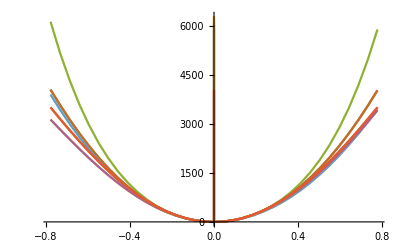

```mathematica
ListLinePlot@Partition[get1dProjection[dataCvector,3],Length[get1dProjection[dataCvector,1]]/11]
```

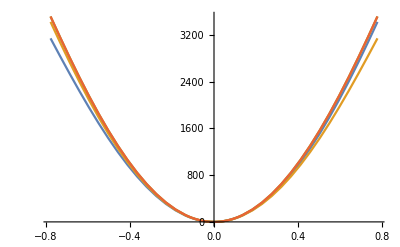

```mathematica
ListLinePlot@Partition[get1dProjection[dataCvector,2],Length[get1dProjection[dataCvector,1]]/11][[8;;11]]
```

```mathematica
varGetter[arg_]:=If[Length@arg==2,arg[[2]],If[Length@arg==3,arg,0]]
VnnnCoeffsVars=varGetter/@VnnnCoeffs;
VnnCoeffsVars=varGetter/@VnnCoeffs;
VperfCoeffsVars=varGetter/@VperfCoeffs;

nlmCnnn=NonlinearModelFit[dataCvector,{Vnnn[x,y,z]},VnnnCoeffsVars,{x,y,z}]
nlmZrnn=NonlinearModelFit[dataZrvector,{Vnn[x,y,z]},VnnCoeffsVars,{x,y,z}]
nlmCperf=NonlinearModelFit[dataCvectorPerf,{Vperf[x,y,z]},VperfCoeffsVars,{x,y,z}]
nlmZrperf=NonlinearModelFit[dataZrvectorPerf,{Vperf[x,y,z]},VperfCoeffsVars,{x,y,z}]
```

FittedModel[6.58507 x+2610.81 x^2-136.485 x^3+«65»+61.3824 z^5-535.105 x z^5-4070.85 z^6]

FittedModel[28.8619 x+«38»+426.196 y^2 z^4-8080.12 z^6]

FittedModel[3803.47 x^2+18997.2 x^4-4833.44 x^6+«27»]

FittedModel[5462.41 x^2+26726.9 x^4-8008.79 x^6+«27»]

```mathematica
(*4th*)
nlmCnnn["RSquared"]
```

0.934101

```mathematica
(*6th*)
nlmCnnn["RSquared"]
```

0.993852

```mathematica
(*8th*)
nlmCnnn["RSquared"]
```

0.998538

```mathematica
(*10th*)
nlmCnnn["RSquared"]
```

0.912067

```mathematica
(*12th*)
nlmCnnn["RSquared"]
```

0.993675

```mathematica
nlmCnnnF[xx_,yy_,zz_]:=nlmCnnn["BestFit"]/.{x->xx,y->yy,z->zz}
nlmZrnnF[xx_,yy_,zz_]:=nlmZrnn["BestFit"]/.{x->xx,y->yy,z->zz}
nlmCperfF[xx_,yy_,zz_]:=nlmCperf["BestFit"]/.{x->xx,y->yy,z->zz}
nlmZrperfF[xx_,yy_,zz_]:=nlmZrperf["BestFit"]/.{x->xx,y->yy,z->zz}
```

```mathematica
Plot3D[nlmCnnnF[0,y,z],{y,-1,1},{z,-1,1}]
Plot3D[nlmCnnnF[y,0,z],{y,-1,1},{z,-1,1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[nlmCnnnF[y,0,z],{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[nlmZrnnF[y,0,z],{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[nlmZrnnF[x,y,0],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

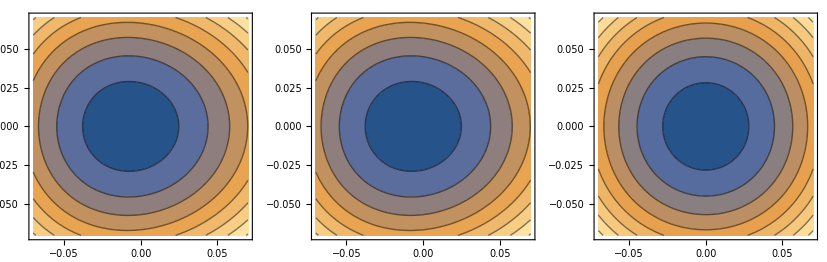

```mathematica
GraphicsGrid@{{With[{a=0.07},ContourPlot[nlmZrnnF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.07},ContourPlot[nlmZrnnF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.07},ContourPlot[nlmZrnnF[0,y,z],{y,-a,a},{z,-a,a}]]}}
```

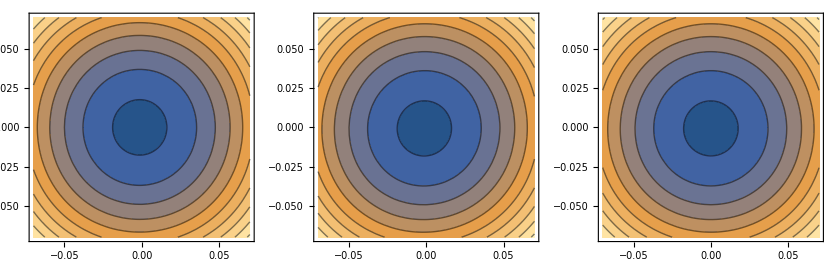

```mathematica
GraphicsGrid@{{With[{a=0.07},ContourPlot[nlmCnnnF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.07},ContourPlot[nlmCnnnF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.07},ContourPlot[nlmCnnnF[0,y,z],{y,-a,a},{z,-a,a}]]}}
```

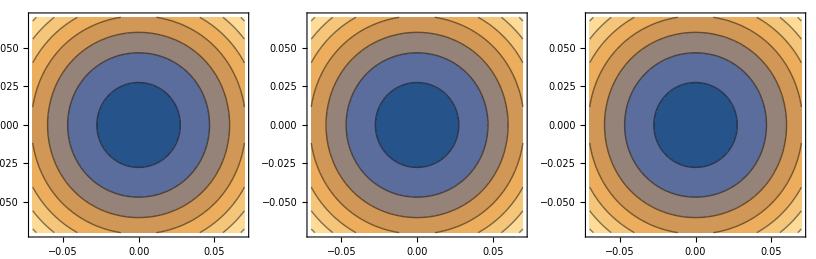

```mathematica
GraphicsGrid@{{With[{a=0.07},ContourPlot[nlmCperfF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.07},ContourPlot[nlmCperfF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.07},ContourPlot[nlmCperfF[0,y,z],{y,-a,a},{z,-a,a}]]}}
```

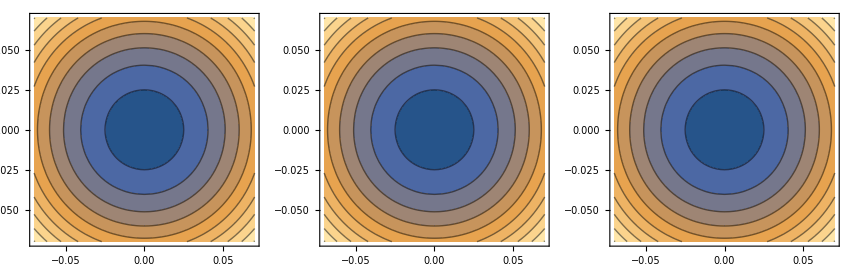

```mathematica
GraphicsGrid@{{With[{a=0.07},ContourPlot[nlmZrperfF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.07},ContourPlot[nlmZrperfF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.07},ContourPlot[nlmZrperfF[0,y,z],{y,-a,a},{z,-a,a}]]}}
```

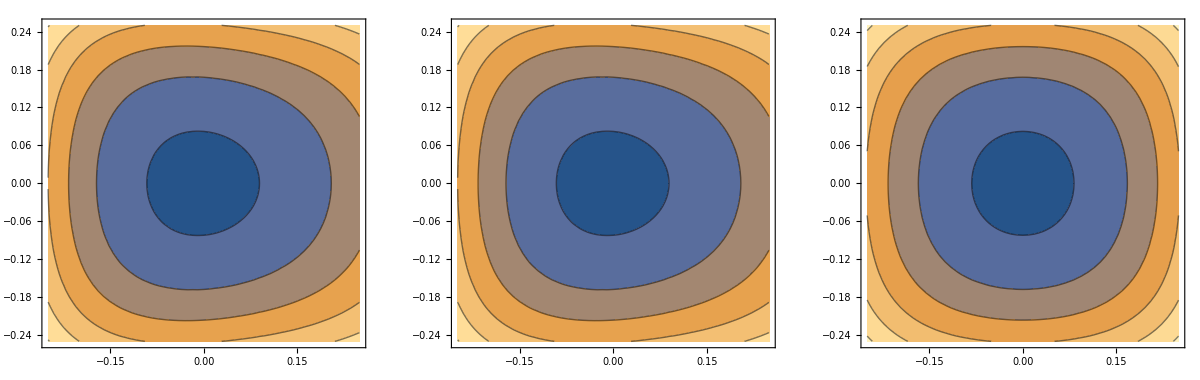

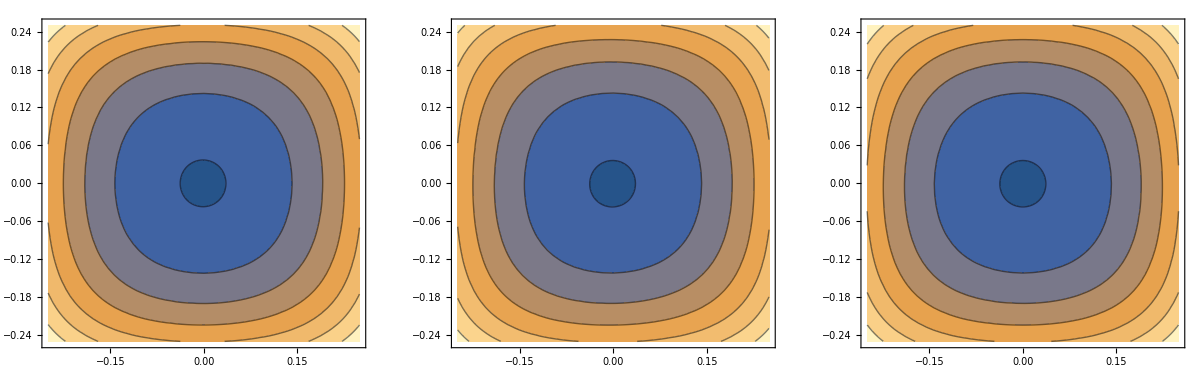

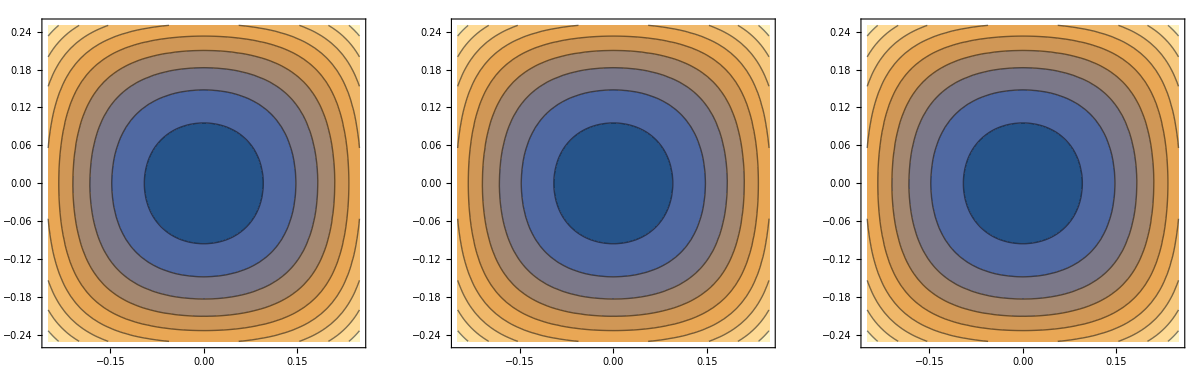

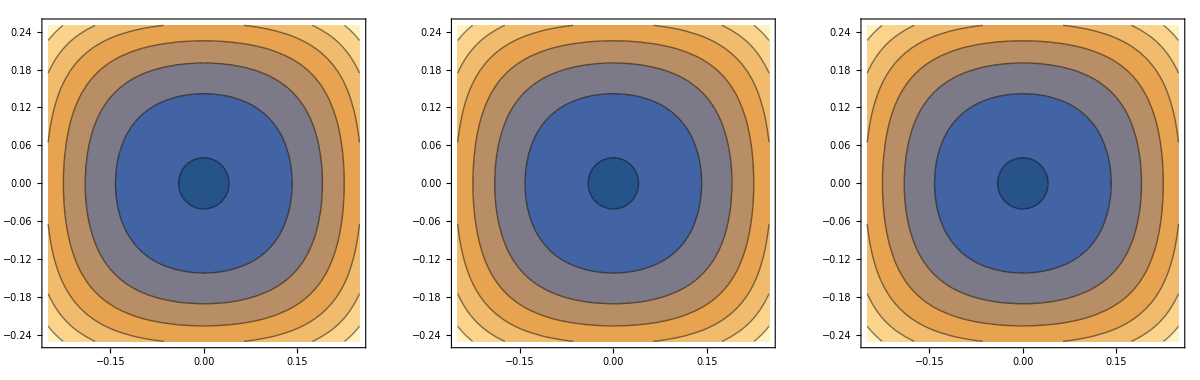

```mathematica
GraphicsGrid@{{With[{a=0.25},ContourPlot[nlmZrnnF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.25},ContourPlot[nlmZrnnF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.25},ContourPlot[nlmZrnnF[0,y,z],{y,-a,a},{z,-a,a}]]}}
GraphicsGrid@{{With[{a=0.25},ContourPlot[nlmCnnnF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.25},ContourPlot[nlmCnnnF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.25},ContourPlot[nlmCnnnF[0,y,z],{y,-a,a},{z,-a,a}]]}}
GraphicsGrid@{{With[{a=0.25},ContourPlot[nlmCperfF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.25},ContourPlot[nlmCperfF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.25},ContourPlot[nlmCperfF[0,y,z],{y,-a,a},{z,-a,a}]]}}
GraphicsGrid@{{With[{a=0.25},ContourPlot[nlmZrperfF[x,y,0],{x,-a,a},{y,-a,a}]],With[{a=0.25},ContourPlot[nlmZrperfF[x,0,z],{x,-a,a},{z,-a,a}]],With[{a=0.25},ContourPlot[nlmZrperfF[0,y,z],{y,-a,a},{z,-a,a}]]}}
```

```mathematica
Plot[{nlmCnnnF[x,0,0],nlmCnnnF[0,x,0],nlmCnnnF[0,0,x]},{x,-1,1}]
```

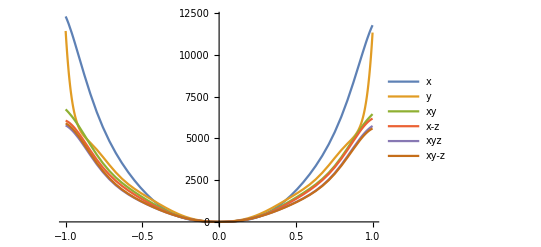

```mathematica
Plot[{nlmCnnnF[x,0,0],nlmCnnnF[0,x,0],nlmCnnnF[x/Sqrt[2],x/Sqrt[2],0],nlmCnnnF[x/Sqrt[2],0,-x/Sqrt[2]],nlmCnnnF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]],nlmCnnnF[x/Sqrt[3],x/Sqrt[3],-x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","y","xy","x-z","xyz","xy-z"}]
```

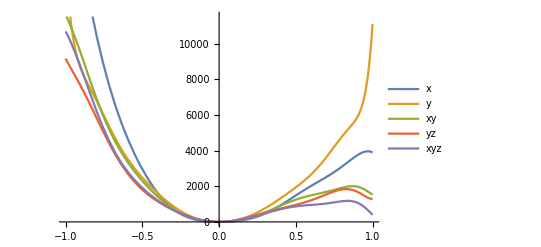

```mathematica
Plot[{nlmZrnnF[x,0,0],nlmZrnnF[0,x,0],nlmZrnnF[x/Sqrt[2],x/Sqrt[2],0],nlmZrnnF[0,x/Sqrt[2],x/Sqrt[2]],nlmZrnnF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","y","xy","yz","xyz"}]
```

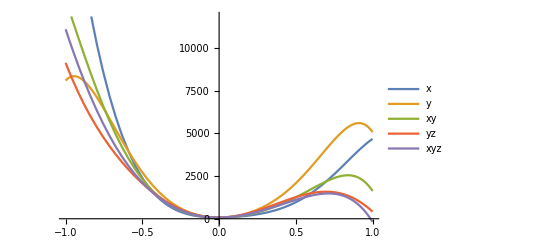

```mathematica
Plot[{nlmZrnnF[x,0,0],nlmZrnnF[0,x,0],nlmZrnnF[x/Sqrt[2],x/Sqrt[2],0],nlmZrnnF[0,x/Sqrt[2],x/Sqrt[2]],nlmZrnnF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","y","xy","yz","xyz"}]
```

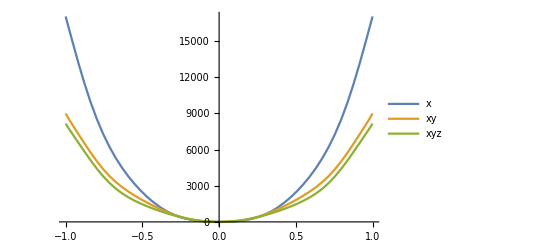

```mathematica
Plot[{nlmCperfF[x,0,0],nlmCperfF[x/Sqrt[2],x/Sqrt[2],0],nlmCperfF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","xy","xyz"}]
```

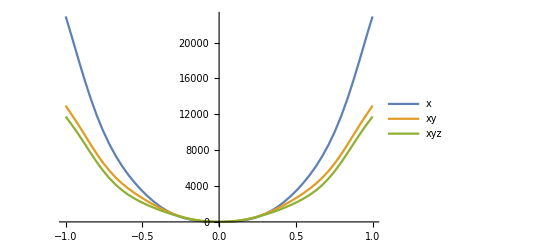

```mathematica
Plot[{nlmZrperfF[x,0,0],nlmZrperfF[x/Sqrt[2],x/Sqrt[2],0],nlmZrperfF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","xy","xyz"}]
```

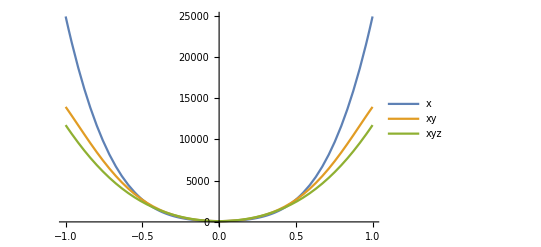

```mathematica
Plot[{nlmZrperfF[x,0,0],nlmZrperfF[x/Sqrt[2],x/Sqrt[2],0],nlmZrperfF[x/Sqrt[3],x/Sqrt[3],x/Sqrt[3]]},{x,-1,1},PlotLegends->{"x","xy","xyz"}]
```

```mathematica
With[{a=0.35},ContourPlot3D[nlmCnnnF[x,y,z]==400,{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

```mathematica
With[{a=0.35},ContourPlot3D[nlmZrnnF[x,y,z]==400,{x,-a,a},{y,-a,a},{z,-a,a},Contours->1]]
```

-Graphics3D-

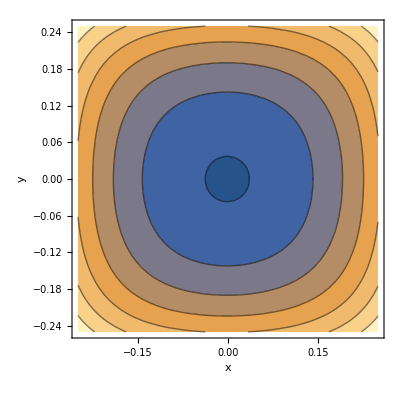

```mathematica
With[{p=0.25},ContourPlot[nlmCnnnF[x,y,0],{x,-p,p},{y,-p,p},FrameLabel->{"x","y"}]]
```

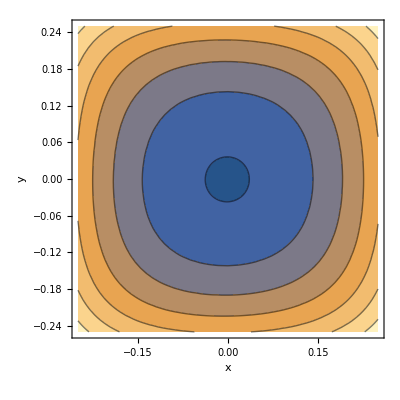

```mathematica
With[{p=0.25},ContourPlot[nlmCnnnF[x,0,z],{x,-p,p},{z,-p,p},FrameLabel->{"x","y"}]]
```

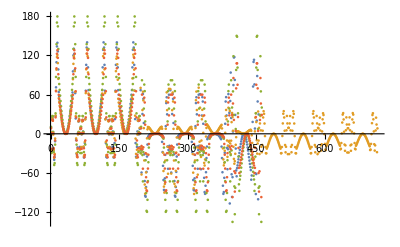

```mathematica
residuals=With[{arg="FitResiduals"},Table[nlms[[i]][arg],{i,1,4}]];
ListPlot@residuals
```

```mathematica
nlmCnnn[0,0,0]
nlmZrnn[0,0,0]
nlmCperf[0,0,0]
nlmZrperf[0,0,0]
```

46.7687

71.7963

67.381

91.9265

```mathematica
nlms={nlmZrnn,nlmCnnn,nlmZrperf,nlmCperf};
nlmsNames={"nlmZrnn","nlmCnnn","nlmZrperf","nlmCperf"};
rVals=With[{arg="RSquared"},Table[nlms[[i]][arg],{i,1,4}]]
residuals=With[{arg="FitResiduals"},Table[nlms[[i]][arg],{i,1,4}]];
```

{0.99981,0.999797,0.999826,0.99981}

```mathematica
nlms={nlmZrnn,nlmCnnn,nlmZrperf,nlmCperf};
nlmsNames={"nlmZrnn","nlmCnnn","nlmZrperf","nlmCperf"};
rVals=With[{arg="RSquared"},Table[nlms[[i]][arg],{i,1,4}]]
residuals=With[{arg="FitResiduals"},Table[nlms[[i]][arg],{i,1,4}]];
```

{0.994837,0.993418,0.994956,0.993631}

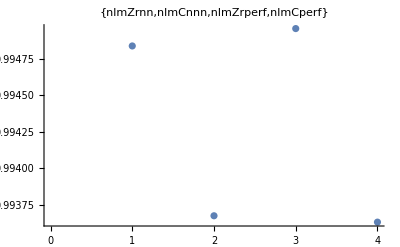

```mathematica
ListPlot[Evaluate@rVals,PlotLabel->nlmsNames]
```

```mathematica
nlmCperf["EstimatedVariance"]
```

2523.06

```mathematica
nlmCperf["ANOVATable"]
```

| DF | SS | MS
Model | 83 | 5.02587×10^9 | 6.05527×10^7
Error | 379 | 956241. | 2523.06
Uncorrected Total | 462 | 5.02683×10^9 | 
Corrected Total | 461 | 3.53941×10^9 |

```mathematica
nlmCnnn["ANOVATable"]
```

| DF | SS | MS
Model | 251 | 3.91992×10^9 | 1.56172×10^7
Error | 464 | 795632. | 1714.73
Uncorrected Total | 715 | 3.92072×10^9 | 
Corrected Total | 714 | 2.67939×10^9 |

```mathematica
nlmZrnn["ANOVATable"]
```

| DF | SS | MS
Model | 139 | 5.71178×10^9 | 4.1092×10^7
Error | 316 | 1.08759×10^6 | 3441.74
Uncorrected Total | 455 | 5.71287×10^9 | 
Corrected Total | 454 | 3.98094×10^9 |

```mathematica
3000/(4*10^7)//N
```

0.000075

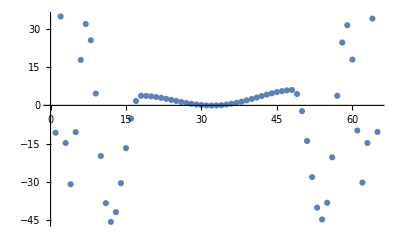

```mathematica
ListPlot[Partition[residuals[[2]],65][[7]]]
```

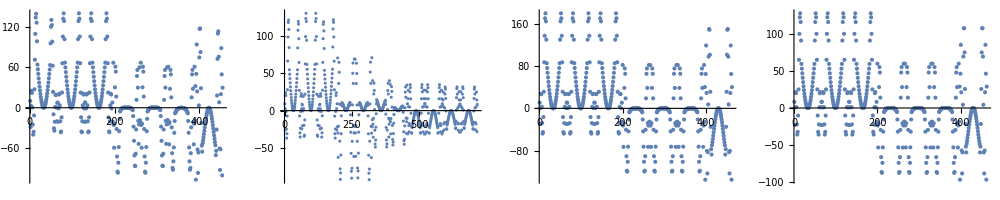

```mathematica
GraphicsGrid[{{ListPlot@residuals[[1]],ListPlot@residuals[[2]],ListPlot@residuals[[3]],ListPlot@residuals[[4]]}},ImageSize->1000]
```

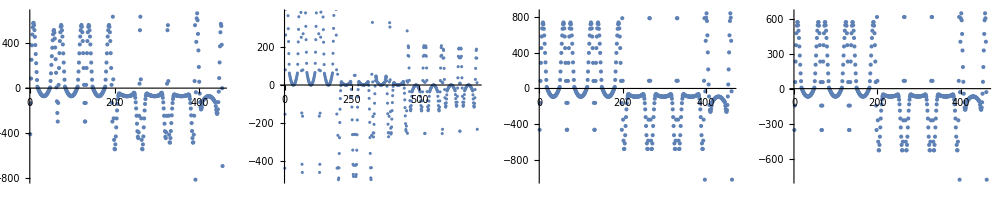

```mathematica
GraphicsGrid[{{ListPlot@residuals[[1]],ListPlot@residuals[[2]],ListPlot@residuals[[3]],ListPlot@residuals[[4]]}},ImageSize->1000]
```

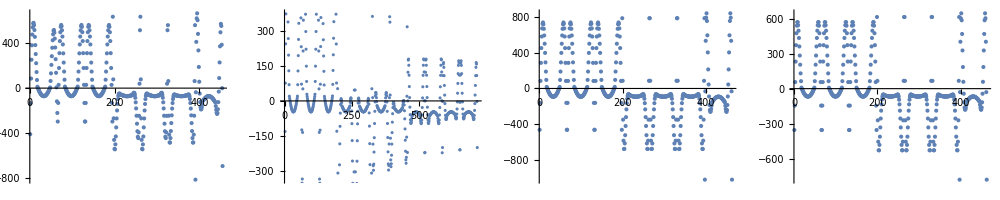

```mathematica
GraphicsGrid[{{ListPlot@residuals[[1]],ListPlot@residuals[[2]],ListPlot@residuals[[3]],ListPlot@residuals[[4]]}},ImageSize->1000]
```

```mathematica
nlmCnnn["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableMeanSquares,ANOVATableSumsOfSquares,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,EstimatedVariance,FitCurvatureTable,FitCurvatureTableEntries,FitResiduals,Function,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterBias,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals}

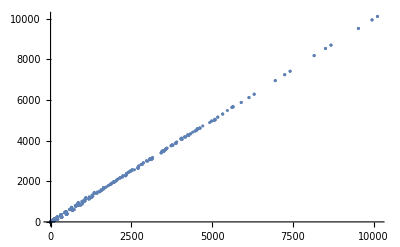

```mathematica
ListPlot@Transpose@nlmCnnn[{"Response","PredictedResponse"}]
```

```mathematica
Norm@nlmCnnn["Data"][[1]][[1;;3]]
```

0.915

```mathematica
nlmCnnn["PredictedResponse"]//Dimensions
```

{715}

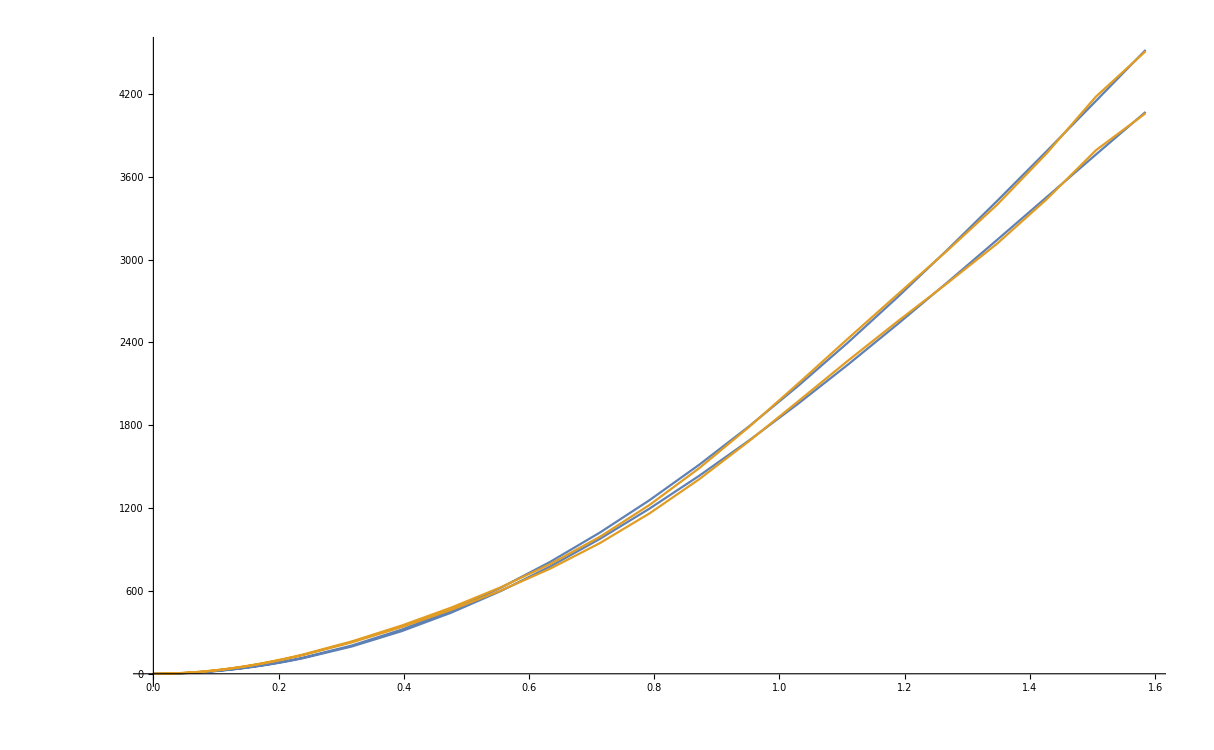

```mathematica
ListLinePlot[{Partition[Transpose@{Norm/@Transpose@Transpose[nlmCnnn["Data"]][[1;;3]],Transpose[nlmCnnn["Data"]][[4]]},65][[8]],Partition[Transpose@{Norm/@Transpose@Transpose[nlmCnnn["Data"]][[1;;3]],nlmCnnn["PredictedResponse"]},65][[8]]}]
```

```mathematica
ListLinePlot[{Partition[Transpose@{Norm/@Transpose@Transpose[nlmCnnn["Data"]][[1;;3]],Transpose[nlmCnnn["Data"]][[4]]},65][[1]],Partition[Transpose@{Norm/@Transpose@Transpose[nlmCnnn["Data"]][[1;;3]],nlmCnnn["PredictedResponse"]},65][[1]]}];
```